```mathematica
f[x_]:=a Sin[b x]+c Cos[d x]+Cos[x]+4.5
a=1.4
b=3
c=1.2
d=4.5
N[Solve[f'[x+4.077]==0&&x>0&&x<5,x, Reals]]
x0=1.1
x1=2.031982161048468
x2=3.690200140461272
x3=0.8924904834689227
off=0.2
s=15
s1=15
Plot[f[x+4.077],{x,0,5}, Ticks->None, Epilog->{Point[{x0,f[x0+4.077]}],Text[Style["C",s],{x0,f[x0+4.077]+off},{0,-1}],Point[{x1,f[x1+4.077]}],Text[Style["C_1",s],{x1,f[x1+4.077]+off},{0,-1}],Point[{x2,f[x2+4.077]}],Text[Style["C_0",s],{x2,f[x2+4.077]+off},{0,-1}],Point[{x3,f[x3+4.077]}],Text[Style["C_2",s],{x3,f[x3+4.077]+off},{0,-1}]}, FrameLabel->{Style["Configuraciones",s1], Style["F",s1]}]
```

## Hexagonos

0.06

-Graphics-

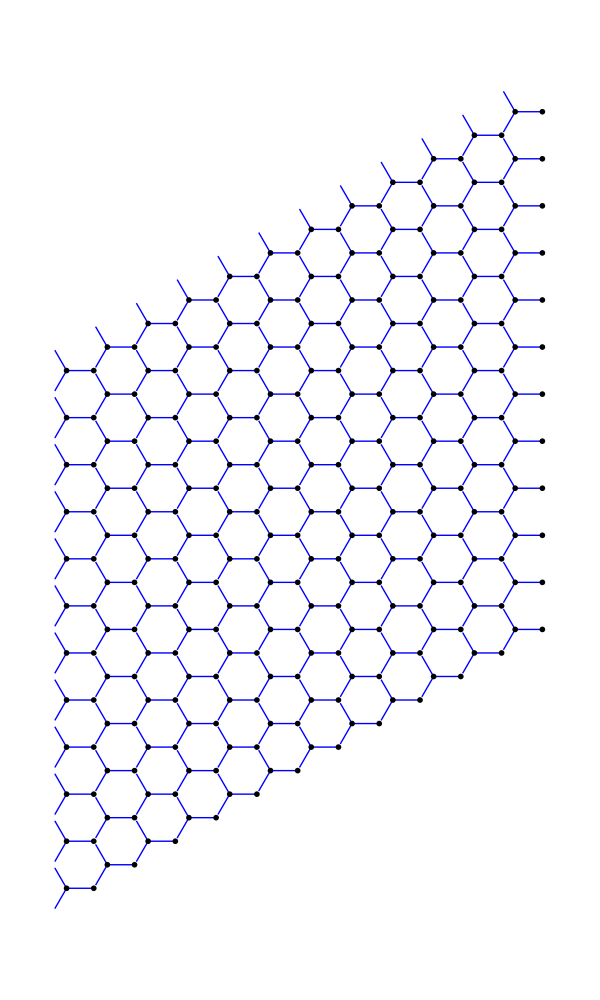

```mathematica
tam=0.06
unitCell[x_,y_]:={Blue,Line[{{x,y},{x+2/3 Sin[120 Degree],y}}],Blue,Line[{{x,y},{x-Sin[30 Degree]/2,y+Cos[30 Degree]/2}}],Blue,Line[{{x,y},{x-Sin[30 Degree]/2,y-Cos[30 Degree]/2}}],Black,Disk[{x,y},tam],Black,Disk[{x+2/3 Sin[120 Degree],y},tam]}
Graphics[unitCell[0,0],ImageSize->100]
Graphics[Block[{unitVectA={Sin[60Degree],Cos[60Degree]},unitVectB={0,1}},Table[unitCell@@(unitVectA j+unitVectB k),{j,-12,-1},{k,1,12}]],ImageSize->600]
```

Cuadrados

0.06

-Graphics-

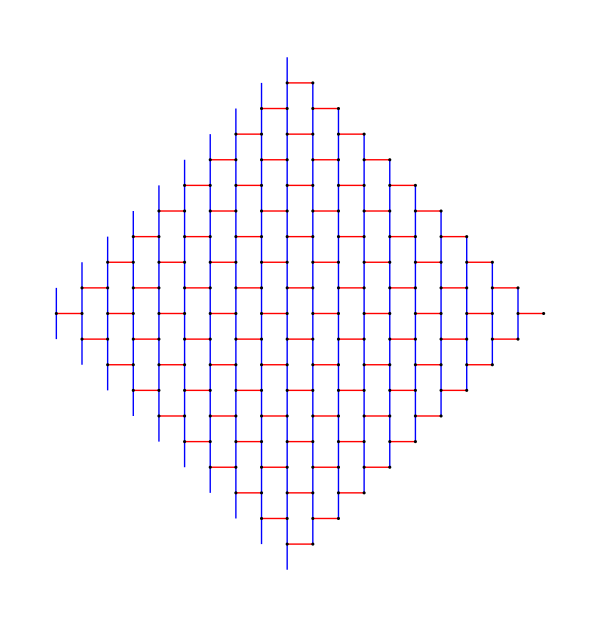

```mathematica
tam=0.06
unitCell2[x_,y_]:={Red,Line[{{x,y},{x+1,y}}],Blue,Line[{{x,y},{x,y+1}}],Blue,Line[{{x,y},{x,y-1}}],Black,Disk[{x,y},tam],Black,Disk[{x+1,y},tam]}
Graphics[unitCell2[0,0],ImageSize->100]
Graphics[Block[{unitVectA={-1,1},unitVectB={-1,-1}},Table[unitCell2@@(unitVectA j+unitVectB k),{j,-10,-1},{k,1,10}]],ImageSize->600]
```

0.06

-Graphics-

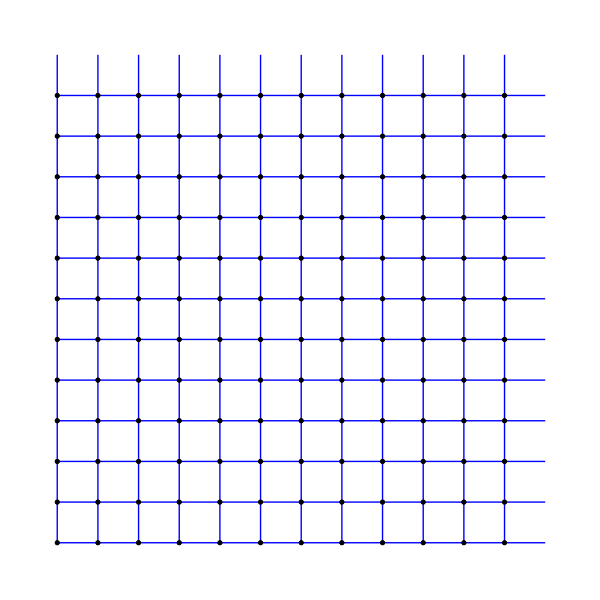

```mathematica
tam=0.06
unitCell[x_,y_]:={Blue,Line[{{x,y},{x+1,y}}],Blue,Line[{{x,y+1},{x,y}}],Blue,Line[{{x,y},{x,y}}],Black,Disk[{x,y},tam],Black,Disk[{x,y},tam]}
Graphics[unitCell[0,0],ImageSize->100]
Graphics[Block[{unitVectA={1,0},unitVectB={0,1}},Table[unitCell@@(unitVectA j+unitVectB k),{j,-12,-1},{k,1,12}]],ImageSize->600]
```

## Archivos y fit

FittedModel[0.518899-3.06213 Tanh[2.1399-3.06213 x]+2.58779 Tanh[2.24517-3.06213 x]]

FittedModel[0.605859-8.02672 Tanh[2.12386-8.02672 x]+7.6331 Tanh[2.15328-8.02672 x]]

FittedModel[0.267616+0.00636146 x]

1.53107

4.01336

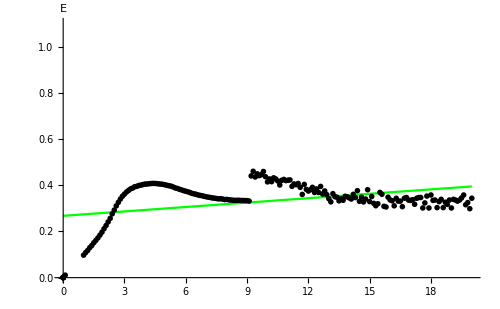

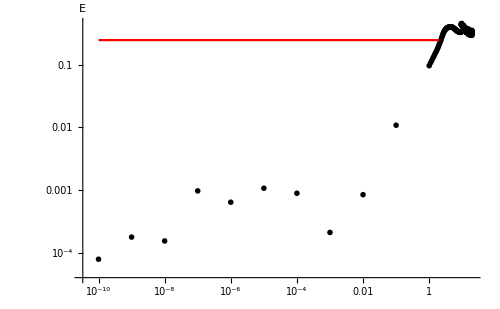

20hexE805.png

20hexE805log.png

```mathematica
data=Import["C:\\Users\\pcard\\OneDrive\\4.ba\\TFG\\Python TFG\\IsingModel\\QAhexenergia821.dat"];
data2=Import["C:\\Users\\pcard\\OneDrive\\4.ba\\TFG\\Python TFG\\IsingModel\\hexenergia821.dat"];
data3=Import["C:\\Users\\pcard\\OneDrive\\4.ba\\TFG\\Python TFG\\IsingModel\\hexenergia8200.5.dat"];
base=a+2J  Tanh[2 J  x-d]+e Tanh[2 J  x -i];
base2=a+b x;
l=Length[data];
l2=Length[data2];
l3=Length[data3];
s=500;
n=8;
SetDirectory["C:\\Users\\pcard\\OneDrive\\4.ba\\TFG\\Documento Latex"];
tipo="E";
c1="1";
c2="05";
nombre="20hex";
nombre1=nombre<>tipo<>ToString [n]<>c1;
nombre1log=nombre<>tipo<>ToString [n]<>c1<>"log";
nombre2=nombre<>tipo<>ToString [n]<>c2;
nombre2log=nombre<>tipo<>ToString [n]<>c2<>"log";
nombre3=nombre<>tipo<>ToString [n]<>c2;
nombre3log=nombre<>tipo<>ToString [n]<>c2<>"log";
nombrecomp=nombre<>tipo<>ToString [n]<>c1<>"comp";
nombrecomplog=nombre<>tipo<>ToString [n]<>c1<>"complog";
absdata=Table[{data[[i]][[1]],Abs[data[[i]][[2]]/data[[l]][[2]]]},{i,1,l}];
absdata2=Table[{data2[[i]][[1]],Abs[data2[[i]][[2]]/data2[[l2]][[2]]]},{i,1,l2}];
absdata3=Table[{data3[[i]][[1]],Abs[data3[[i]][[2]]]},{i,1,l3}];
f=NonlinearModelFit[absdata,base,{a,J,d,e,i},x]
f2=NonlinearModelFit[absdata2,base,{a,J,d,e,i},x]
f3=NonlinearModelFit[absdata3,base2,{a,b},x]
J1=J/. f["BestFitParameters"]
J2=J/. f2["BestFitParameters"]
linea=Table[{data[[i]][[1]],2/n},{i,1,l}];

rango={{0,20},{0,1.1}};

plot=Show[Plot[f[x],{x,0,20},PlotRange->rango,PlotStyle->Blue,AxesLabel->{Style["",Large], Style[tipo,Large]}],ListPlot[absdata,PlotStyle->Black], ImageSize->s];
plotl=Show[ListLogLogPlot[absdata,PlotStyle->{Black},AxesLabel->{Style["",Large], Style[tipo,Large]},ImageSize->s]];


plot2=Show[Plot[f2[x],{x,0,20},PlotRange->rango,PlotStyle->Blue,AxesLabel->{Style["",Large], Style[tipo,Large]}],ListPlot[absdata2,PlotStyle->Black], ImageSize->s];
plot2l=Show[ListLogLogPlot[absdata2,PlotStyle->{Black},AxesLabel->{Style["",Large], Style[tipo,Large]},ImageSize->s]];

(*plot3=Show[Plot[{f[x],f2[x]},{x,0,20},PlotRange->rango,PlotStyle->{Blue, Red},AxesLabel->{Style["",Large], Style[tipo,Large]}],ListPlot[{absdata,absdata2},PlotStyle->{Black, Gray}], ImageSize->s]
plot3l=Show[ListLogLogPlot[{absdata,absdata2}, PlotRange->Full,PlotStyle->{Black, Gray},AxesLabel->{Style["",Large], Style[tipo,Large]},ImageSize->s], ListLogLogPlot[linea, PlotStyle->Red,Joined->True], ImageSize->s]*)
plot2=Show[Plot[f3[x],{x,0,20},PlotRange->rango,PlotStyle->Blue,AxesLabel->{Style["",Large], Style[tipo,Large]}],ListPlot[absdata3,PlotStyle->Black], ImageSize->s];
plot2l=Show[ListLogLogPlot[absdata3,PlotStyle->{Black},AxesLabel->{Style["",Large], Style[tipo,Large]},ImageSize->s]];


plot3=Show[Plot[{f3[x]},{x,0,20},PlotRange->rango,PlotStyle->{Green},AxesLabel->{Style["",Large], Style[tipo,Large]}],ListPlot[{absdata3},PlotStyle->{ Black},PlotMarkers->{"OpenMarkers"}], ImageSize->s]
plot3l=Show[ListLogLogPlot[{absdata3}, PlotRange->Full,PlotStyle->{ Black},PlotMarkers->{"OpenMarkers"},AxesLabel->{Style["",Large], Style[tipo,Large]},ImageSize->s], ListLogLogPlot[linea, PlotStyle->Red,Joined->True], ImageSize->s]



(*Export[nombre1<>".png",plot]
Export[nombre1log<>".png",plotl]
Export[nombre2<>".png",plot2]
Export[nombre2log<>".png",plot2l]
Export[nombre2<>"J.dat",{ToString[{nombre2,J2}],ToString[f2,FormatType->TeXForm]}]
Export[nombrecomp<>".png",plot3]
Export[nombrecomplog<>".png",plot3l]
Export[nombre1<>"J.dat",{ToString[{nombre1,J1}],ToString[f,FormatType->TeXForm]}]*)
Export[nombre3<>".png",plot3]
Export[nombre3log<>".png",plot3l]
```